Links to all notebooks

basicsDMDO
calc1 calc2 calc3 calc4 calc5
matrices
ode
odesys

# Calculus 5 Derivatives and integrals

```mathematica
D,f',f",
Integrate, NIntegrate
```

## The derivative of a function

Derivatives of functions can be calculated with the command D. It can be used for functions of one or more variables and also for first or higher order (partial) derivatives. Here we will only consider one variable functions.

```mathematica
{{?D}, {□}}
```

{{},{□}}

### Examples

Mathematica can produce derivatives of all standard mathematical functions.Here you may use symbolic notation for derivatives in stead of D. For example ∂_x Sin[x] in stead of D[Sin[x],x] and in the case of 2nd order derivatives ∂_{x,2} Sin[x] in stead of D[Sin[x],x,x].

```mathematica
D[Sin[x], x]
```

```mathematica
D[(3 y^3+7 y^2-2 y+8), y]
```

```mathematica
D[ArcTan[x], x]
```

```mathematica
D[Log[x], x]
```

```mathematica
D[Log[x], {x,2}]
```

```mathematica
D[Log[x], {x,3}]
```

It is even possible to use the familiar 'prime' for differentiation:

```mathematica
Sin'[x]
```

```mathematica
f[x_]:=x^2 ⅇ^-x
```

```mathematica
f'[x]
```

```mathematica
f''[x]
```

```mathematica
Derivative[3][f][x]
```

#### Note: order of evaluation!

The D - command lets Mathematica evaluate the derivative of the expression in the first position with respect to the variable mentioned in the second position, so D[Sin[x],x] will give Cos[x], but cannot be considered as the derivative function! So the following will not work:

```mathematica
dsin[x_]:=D[Sin[x],x]
```

```mathematica
dsin[3]
```

General::ivar: 3 is not a valid variable.

∂_3 Sin[3]

There is a way out, using Evaluate again, in order to force Mathematica to first evaluate the derivative, before assigning a value to x:

```mathematica
dsin[x_]:=Evaluate[D[Sin[x],x]]
```

```mathematica
dsin[3]
```

Cos[3]

Actually this is exactly what the prime operation does:

```mathematica
Sin'[3]
```

Cos[3]

Of course you can also use the the command ReplaceAll, or the corresponding shorthand replacement-operator /. for the control of the order of evaluation:

```mathematica
D[Sin[x],x]/.{x->3}
```

We conclude that there is an essential difference in the use of D and prime!

### Rules of differentiation

You can 'simulate' the rules of differentiation like product-rule and chain-rule.

```mathematica
Clear[f,g]
```

The product-rule:

```mathematica
D[(f[x] g[x]), x]
```

g[x] f'[x]+f[x] g'[x]

Quotient-rule:

```mathematica
D[f[x]/g[x], x]
```

f'[x]/g[x]-(f[x] g'[x])/g[x]^2

And the chain-rule:

```mathematica
D[f[g[x]], x]
```

f'[g[x]] g'[x]

### Geometric interpretation: tangent-line

As you know, the derivative of a function f at a certain point can be considered as the slope of the tangent line at that point to the graph of the function.
Let us consider the function f defined by:

```mathematica
f[x_]:=x^2 ⅇ^-x
```

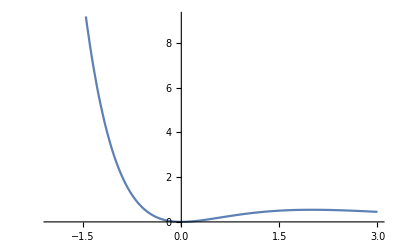

```mathematica
Plot[f[x],{x,-2,3}]
```

At  x=1 the tangent line has slope f'(1) and, as the point (1,f(1)) is on the tangent line, the equation for this line is y=f(1)+f'(1) (x-1). Now we will plot this line in the graph of f. Colour it differently or make it dashed, so that you can discern it clearly.

```mathematica
g[x_]:=f[1]+f'[1] (x-1)
```

```mathematica
g[x]
```

1/ⅇ+(-1+x)/ⅇ

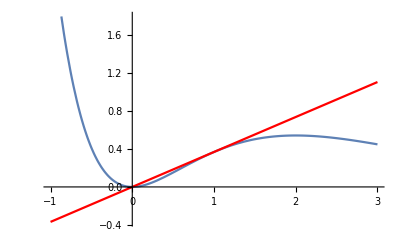

```mathematica
Plot[{f[x],g[x]},{x,-1,3},PlotStyle->{{},RGBColor[1,0,0]}]
```

## Partial differentiation

For partial differentiation we use the same command, D, as for differentiating 1 variable functions.
Let us look at an example.

First we define a function, e.g.:

```mathematica
f[x_,y_]:=x y (1-x^2-y^2)
```

We will subsequently determine the partial derivatives w.r.t. x and y: The commands Simplify and Expand can help you to make expressions more readible.

```mathematica
D[f[x,y], x]
```

-2 x^2 y+y (1-x^2-y^2)

```mathematica
Simplify[%]
```

-y (-1+3 x^2+y^2)

```mathematica
Simplify[D[f[x,y], y]]
```

-x (-1+x^2+3 y^2)

The second order partial derivatives follow obviously, e.g. (f^")_xx:

```mathematica
D[f[x,y], x,x]
```

-6 x y

As before this expression can be evaluated at a point (a,b) with the help of the command ReplaceAll or the replacement-operator /.{x→a,y→b}, where a and b may be numbers as well as variables (names):

```mathematica
D[f[x,y], x]/.{x->2,y->b}
```

-8 b+b (-3-b^2)

```mathematica
Simplify[%]
```

-b (11+b^2)

Another way to determine a partial derivative at a point is:
first define the partial derivative as a function of (x,y) and then ask for its value at that point:

```mathematica
f1[x_,y_]:=D[f[x,y], x]
```

```mathematica
f1[a,b]
```

-2 a^2 b+b (1-a^2-b^2)

```mathematica
f1[a,1]
```

-3 a^2

```mathematica
f1[2,b]
```

General::ivar: 2 is not a valid variable.

∂_2 (2 b (-3-b^2))

Again there is a problem, so be careful! We want Mathematica to first evaluate the derivative and then assign the value x=2. This can be achieved as follows by a slight adaptation of the definition of the partial derivative funtion, using the command Evaluate again, that organizes the order of evaluation, i.e. first evaluate the derivative:

```mathematica
f1[x_,y_]:=Evaluate[D[f[x,y], x]]
```

```mathematica
f1[2,b]
```

-8 b+b (-3-b^2)

## Applications of the derivative

### Convexity and concavity

Applications of the derivative lie in the field of convexity/concavity of functions and optimization of functions. Let us consider a polynomial function of degree 4 and try to determine where this function is convex or concave and where a maximum or a minimum value is attained.

```mathematica
f[x_]:=(x+2) (x+1) (x-1) (x-2)
```

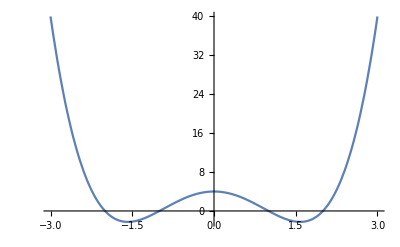

```mathematica
Plot[f[x],{x,-3,3}]
```

The first derivative shows us where the function increases or decreases, the second derivative where it is convex or concave. Let us plot f, f', and f" in one graph, f black, f' red and f" blue. Now the properties of these derivatives can clearly be observed.

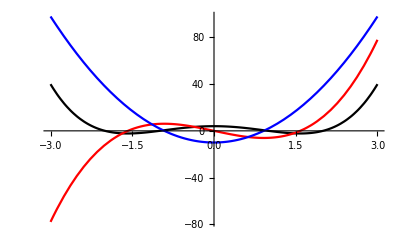

```mathematica
Plot[{f[x],f'[x],f''[x]},{x,-3,3},PlotStyle->{RGBColor[0,0,0],RGBColor[1,0,0],RGBColor[0,0,1]}]
```

In order to be able to exactly determine the intervals where f increases, decreases, is convex or concave we have to find the zeros of f' and f''.

```mathematica
Solve[f'[x]==0,x]
```

{{x→0},{x→-√(5/2)},{x→√(5/2)}}

From these values and the graph we can conclude, that
	f  increases on the intervals [-√(5/2),0] and [√(5/2),∞), and
	f decreases on the intervals (-∞,-√(5/2)] and [0,√(5/2)].

```mathematica
Solve[f''[x]==0,x]
```

{{x→-√(5/6)},{x→√(5/6)}}

From these values and the graph we can conclude, that
	f  is convex on the intervals (-∞,-√(5/6)] and [√(5/6),∞), and
	f is concave on the interval [-√(5/6),√(5/6)].

## The integral of a function

Mathematica can determine definite as well as indefinite integrals (primitives). For both operations the same command Integrate is used. The indefinite integral is evaluated without the integration constant, i.e. this constant is taken to be zero. Besides, for definite integrals the command NIntegrate is available for numerical approximations.
As we know, differentiating a primitive should yield the original function, a way to check results.

```mathematica
?Integrate
```

```mathematica
?NIntegrate
```

### Examples

```mathematica
∫x^2/(√(x^3+9))ⅆx
```

(2 √(9+x^3))/3

Check:

```mathematica
∂_x %
```

x^2/(√(9+x^3))

```mathematica
∫_-1^1 x^2/(√(x^3+9))ⅆx
```

2/3 √2 (-2+√5)

```mathematica
∫Log[x]^2 ⅆx
```

2 x-2 x Log[x]+x Log[x]^2

```mathematica
∫_1^ⅇ Log[x]^2 ⅆx
```

-2+ⅇ

```mathematica
∫x/(x^2-5 x+6)ⅆx
```

-2 Log[2-x]+3 Log[3-x]

```mathematica
∫_0^1 x/(x^2-5 x+6)ⅆx
```

Log[32/27]

```mathematica
∫1/(x^2+x+1)ⅆx
```

(2 ArcTan[(1+2 x)/(√3)])/(√3)

```mathematica
∫_1^4 1/(x^2+x+1)ⅆx
```

-(2 (π-3 ArcTan[3 √3]))/(3 √3)

Or, the numerical value:

```mathematica
NIntegrate[1/(x^2+x+1),{x,1,4}]
```

0.385062

This can also be calculated as follows:

```mathematica
N[∫_1^4 1/(x^2+x+1)ⅆx]
```

0.385062

Often, integrals cannot be evaluated exactly. Then we can only use the numerical approximation.

```mathematica
∫x^-2 Tan[x]ⅆx
```

∫Tan[x]/x^2 ⅆx

```mathematica
∫_1^1.5 x^-2 Tan[x]ⅆx
```

∫_1^1.5 Tan[x]/x^2 ⅆx

```mathematica
NIntegrate[x^-2 Tan[x],{x,1,1.5}]
```

1.18258

We can derive theoretical results:

```mathematica
Clear[f]
```

```mathematica
int=∫_0^(x^2) f[t]ⅆt
```

∫_0^(x^2) f[t]ⅆt

```mathematica
D[int, x]
```

2 x f[x^2]

A final remark: also improper integrals can be evaluated, for unbounded functions as well as for unbounded integration intervals:

```mathematica
∫_1^∞ x ⅇ^-x ⅆx
```

2/ⅇ

```mathematica
∫_0^1 1/(√(1-x))ⅆx
```

2

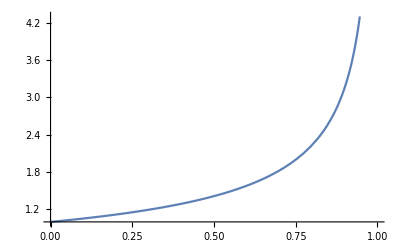

```mathematica
2
Plot[1/(√(1-x)), {x,0,1}]
```

## Exercise

Consider the following function: f(x)=x^5-x^4-6 x^3
a)	Plot this function together with f' and f" in one picture and in different colors.
b)	Give intervals where f increases, decreases, is convex, concave.
c)	Does f have maximum or minimum values, and, if so, where?
d)	Compute the area of the region enclosed by the x-axis and the graph of f 
	for x in [0, 3].
Answers

Links to all notebooks

basicsDMDO
calc1 calc2 calc3 calc4 calc5
matrices
ode
odesys

```mathematica
f[x_]:=x^5-x^4-6 x^3
```

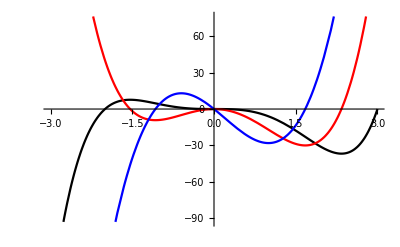

```mathematica
Plot[{f[x],f'[x],f''[x]},{x,-3,3},PlotStyle->{RGBColor[0,0,0],RGBColor[1,0,0],RGBColor[0,0,1]}]
```

```mathematica
Solve[f'[x]==0,x]
```

```mathematica
{{x->0},{x->0},{x->1/5 (2-√94)},{x->1/5 (2+√94)}}
```

```mathematica
Solve[f''[x]==0,x]
```

```mathematica
{{x->0},{x->3/10 (1-√21)},{x->3/10 (1+√21)}}
```

```mathematica
Integrate[f[x],{x,0,3}]
```

-243/5